```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/";
```

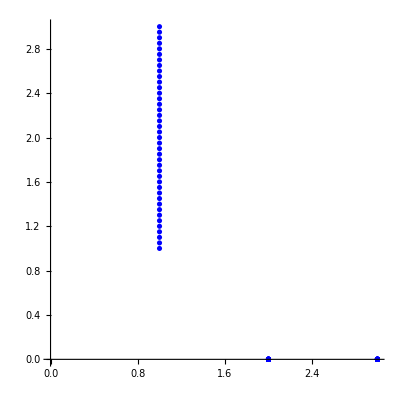

41

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabv=Table[Flatten[{{v[x],0,0}/.repv/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabv,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"v.csv",tabv]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/v.csv

```mathematica
(*write w from ODE to csv file*)
```

```mathematica
tabw=Table[{w[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"w.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/w.csv

```mathematica
(*write σ from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"sigma.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/sigma.csv

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/mu.csv

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabX=Table[Flatten[{{X1[x],X2[x],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabX,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"X.csv",tabX]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/X.csv